## Enhanced Demodulation for Low Latency Audio Pitch Shifting in Frequency Domain Supplementary notebook for equation check

In this Wolfram Mathematica notebook, the equations from paper “Enhanced Demodulation for Low Latency Audio Pitch Shifting in Frequency Domain” are automatically checked. Figure 1 is also generated.
As Mathematica uses some variables beginning with upper-case Latin letters for its internal purposes, variable “N” from paper is represented by “vN” and variable “O” from the paper is represented by “vO” internally.

### Output with general frame overlaps (Subsection 4.1)

General sinusoid equation, centered on bin a of vN sample DFT (inline equation in subsection 4.1) and its exponential representation (Equation 3).
We store the exponential forms without the outside sums applied, applying them only at the end.
The forms are compared for equality (the output should be “True”).

```mathematica
inputSinusoidTrigForm= A*Cos[2π*(n*a)/vN+ϕ];
inputSinusoid=A/2* ⅇ^(ⅈ*q*( 2π*(n*a)/vN+ϕ));
Equal[TrigToExp[inputSinusoidTrigForm],ExpandAll[Sum[inputSinusoid,{q,-1,1,2}]]]
```

True

Running Hanning window in trigonometric and exponential form  (Equation 4).
The forms are compared for equality (the output should be “True”).

```mathematica
runningHanningWindowTrigForm=1/2-1/2 Cos[2*π*(n/vN+p/vO)];
runningHanningWindow=1/4-1/4 ⅇ^(ⅈ*2π*r* (n/vN+p/vO));
Equal[ExpandAll[TrigToExp[runningHanningWindowTrigForm]],ExpandAll[Sum[runningHanningWindow,{r,-1,1,2}]]]
```

True

The “computed form” of Equation 5 is found by multiplying the trigonometric forms of Equation 3 and Equation 4.
The first exponential form used in Equation 5 is also provided.
The forms are compared for equality (the output should be “True”).

```mathematica
analysedResultTrigForm = inputSinusoidTrigForm * runningHanningWindowTrigForm;
analysedResult=A/8*(ⅇ^(ⅈ*q*( 2 π(a*n)/vN+ϕ ))-ⅇ^(ⅈ *(2π(((q*a+r)*n)/vN+(r*p)/vO)+q*ϕ)));
ExpToTrig[ExpandAll[Sum[Sum[analysedResult,{q,-1,1,2}],{r,-1,1,2}]]]
Equal[ExpandAll[TrigToExp[analysedResultTrigForm]], ExpandAll[Sum[Sum[analysedResult,{q,-1,1,2}],{r,-1,1,2}]]]
```

-1/4 A Cos[(2 n π)/vN-(2 a n π)/vN+(2 p π)/vO-ϕ]+1/2 A Cos[(2 a n π)/vN+ϕ]-1/4 A Cos[(2 n π)/vN+(2 a n π)/vN+(2 p π)/vO+ϕ]

True

The second exponential form used in Equation 5 is compared for equality here.

```mathematica
alternativeAnalysedResult=A/8*(ⅇ^(ⅈ*q*( 2 π(a*n)/vN+ϕ ))-ⅇ^(ⅈ *q*(2π(((a+r)*n)/vN+(r*p)/vO)+ϕ)));
Equal[ExpandAll[Sum[Sum[analysedResult,{q,-1,1,2}],{r,-1,1,2}]], ExpandAll[Sum[Sum[alternativeAnalysedResult,{q,-1,1,2}],{r,-1,1,2}]]]
```

True

Now, the running window should be shifted (Equation 6). We introduce a function g(h) which shifts the bins and function u(ϕ) which shifts the phase of the input sinusoid.
The (r*p)/vOpart is not shifted due to the phase shift counteraction in the bin translation routine, which should ensure it stays as it was.
When these functions are identities, the “shifted” running window should be equal to that in Equation 5 (the output should be “True”).

```mathematica
shiftedResult=A/8*(ⅇ^(ⅈ*q*( 2 π*(g[a]*n)/vN+u[ϕ] ))-ⅇ^(ⅈ *q*(2π* ((g[a+r]*n)/vN+(r*p)/vO)+u[ϕ])));
Equal[Sum[Sum[alternativeAnalysedResult,{q,-1,1,2}],{r,-1,1,2}],Sum[Sum[shiftedResult,{q,-1,1,2}],{r,-1,1,2}]/.{g[h_]->h, u[ϕ_]-> ϕ}]
```

True

The output signal equation (Equation 7) is now checked. The synthesis window is the same as the analysis window, we just change the summing variable.

```mathematica
oneFrameSynthesisResult=ExpandAll[FullSimplify[shiftedResult*(runningHanningWindow/.{r->s})]];
oneFrameSynthesisResultPaper=A/32*(ⅇ^(ⅈ*q*( 2 π*(g[a]*n)/vN+u[ϕ] ))-ⅇ^(ⅈ*q*( 2 π*((g[a+r]*n)/vN+(r*p)/vO)+u[ϕ] ))-ⅇ^(ⅈ*( 2 π*(((q*g[a]+s)*n)/vN+(s*p)/vO)+q*u[ϕ] ))+ⅇ^(ⅈ*( 2 π*(((q*g[a+r]+s)*n)/vN+((q*r+s)p)/vO)+q*u[ϕ] )));
oneFrameSynthesisResultExpanded=ExpandAll[Sum[Sum[Sum[oneFrameSynthesisResult,{q,-1,1,2}],{r,-1,1,2}],{s,-1,1,2}]];
oneFrameSynthesisResultPaperExpanded=ExpandAll[Sum[Sum[Sum[oneFrameSynthesisResultPaper,{q,-1,1,2}],{r,-1,1,2}],{s,-1,1,2}]];
Equal[oneFrameSynthesisResultExpanded,oneFrameSynthesisResultPaperExpanded]
```

True

### Output with reasonable frame overlaps (Subsection 4.2)

We simply sum the output signal equations over appropriate overlaps. For frame overlap that is a multiple of 2, we sum  p=0 and p=vO/2. For frame overlap that is a multiple of 4, we sum this result with its copy that is vO/4frames apart.
We then perform the sum and perform full simplification. This should give three cosine terms. The one that is multiplied by 4 should be the wanted one. The other terms are unwanted and result in modulation artifacts. 
Note that the resulting expression no longer depends on frame number p, meaning that the result no longer depends on frame numbers. Therefore, they can just be summed afterwards.

We check that the result is equal to Equation 8.

```mathematica
twoFrameSynthesisResult=oneFrameSynthesisResult +( oneFrameSynthesisResult/.{p->p+vO/2});
fourFrameSynthesisResult=twoFrameSynthesisResult +( twoFrameSynthesisResult/.{p->p+vO/4});
fourFrameOutput =FullSimplify[Sum[Sum[Sum[fourFrameSynthesisResult,{q,-1,1,2}],{r,-1,1,2}],{s,-1,1,2}]];
basicAlgorithmOutput = (vO/4) * fourFrameOutput;
basicAlgorithmOutputPaper=(A*vO)/16*(4*Cos[2π*n/vN*g[a]+u[ϕ]]+Cos[2π*n/vN*(g[a-1]+1)+u[ϕ]]+Cos[2π*n/vN*(g[a+1]-1)+u[ϕ]]);
Equal[basicAlgorithmOutput,basicAlgorithmOutputPaper]
```

True

### Exact Ocean algorithm modulation curve (Subsection 4.3)

To check the exact Ocean algorithm modulation curve in Equation 9, we simply apply the definitions of the functions g(x) and u(x) as used in the Ocean algorithm and divide the actual output by the expected output.

```mathematica
oceanAlgorithmRules={g[a_]->Floor[a*k+1/2],u[ϕ_]->ϕ};

actualOceanOutput=basicAlgorithmOutput/.oceanAlgorithmRules;
expectedOutput = A*Cos[(2 n π g[a])/vN+u[ϕ]];
expectedOceanOutput=expectedOutput/.oceanAlgorithmRules;
oceanModulationCurve=actualOceanOutput/expectedOceanOutput;
oceanModulationCurvePaper=vO/16*(4*Cos[2π*n/vN*Floor[a*k+1/2]+ϕ]+Cos[2π*n/vN*(Floor[(a-1)*k+1/2]+1)+ϕ]+Cos[2π*n/vN*(Floor[(a+1)*k+1/2]-1)+ϕ])/Cos[2 π*n/vN*Floor[a*k+1/2]+ϕ];
Equal[oceanModulationCurve,oceanModulationCurvePaper]
```

True

If the scaling factor k is an integer, the curve simplifies and becomes independent on actual bin number a (Equation 10). If it is equal to one, the curve is constant, as would be expected.

```mathematica
oceanIntegerPitchMultiplierCurve=FullSimplify[oceanModulationCurve, k ∈Integers]
oceanIntegerPitchMultiplierCurve/.{k->1}
```

1/8 vO (2+Cos[(2 (-1+k) n π)/vN])

(3 vO)/8

For scaling factor k=1.5, dependence on bin number a is apparent even when odd and even bins are considered separately (Equation 11).

```mathematica
oneAndHalfEvenBinsModulationCurve=FullSimplify[FullSimplify[(oceanModulationCurve)/.{k->3/2,a-> 2*m}, m ∈ Integers]/.{m->a/2}];
oneAndHalfEvenBinsModulationCurvePaper=vO/16*(5+Cos[π*n/vN*(3a+2)+ϕ]/Cos[π*n/vN*3a+ϕ]);
Equal[oneAndHalfEvenBinsModulationCurve,oneAndHalfEvenBinsModulationCurvePaper]
```

True

```mathematica
oneAndHalfOddBinsModulationCurve=FullSimplify[FullSimplify[(oceanModulationCurve)/.{k->3/2,a-> (2*m+1)}, m ∈ Integers]/.{m->(a-1)/2}];
oneAndHalfOddBinsModulationCurvePaper=vO/16*(5+Cos[π*n/vN*(3a-1)+ϕ]/Cos[π*n/vN*(3a+1)+ϕ]);
Equal[ExpandAll[oneAndHalfOddBinsModulationCurve],ExpandAll[oneAndHalfOddBinsModulationCurvePaper]]
```

True

### Proposed inexact demodulation curve (Subsection 5.1)

Not much can be done with the precise modulation curve as it is heavily dependent on the bin number a. We choose a curve that follows the actual modulation curve reasonably well.

```mathematica
ourCurve= 1/16 vO (4+Cos[2π*n/vN(Floor[(a-1) k+1/2]-Floor[a k+1/2]+1)]+Cos[2 π*n/vN(Floor[(a+1) k+1/2]-Floor[a k+1/2]-1)]) ;
ourDemodulatedOutput=FullSimplify[actualOceanOutput/ourCurve]
```

(A (Cos[ϕ+(2 n π (1+Floor[1/2+(-1+a) k]))/vN]+4 Cos[ϕ+(2 n π Floor[1/2+a k])/vN]+Cos[ϕ+(2 n π (-1+Floor[1/2+k+a k]))/vN]))/(4+Cos[(2 n π (1+Floor[1/2+(-1+a) k]-Floor[1/2+a k]))/vN]+Cos[(2 n π (1+Floor[1/2+a k]-Floor[1/2+k+a k]))/vN])

Our curve simplifies to the same thing as the exact curve if the pitch multiplier k is integer.

```mathematica
FullSimplify[ourCurve,k ∈Integers]
FullSimplify[ourCurve/.{k->1}, a ∈ Integers]
```

1/8 vO (2+Cos[(2 (-1+k) n π)/vN])

(3 vO)/8

In case a=0 and the fractional part of k is not exactly 1/2, the proposed inexact equation and the exact output equation become equivalent. This is due to the properties of the floor function and hard to prove purely in Mathematica.
It is, however, somewhat apparent from the fact that if the fractional part is not exactly 1/2, the two cosine functions below will have the same, just negated, arguments.

```mathematica
FullSimplify[oceanModulationCurvePaper/.{a->0}]
FullSimplify[ourCurve/.{a->0}]
FullSimplify[oceanModulationCurvePaper/.{a->0,k->2.1}]
FullSimplify[ourCurve/.{a->0,k->2.1}]
FullSimplify[oceanModulationCurvePaper/.{a->0,k->2.5}]
FullSimplify[ourCurve/.{a->0,k->2.5}]
```

1/16 vO (4 Cos[ϕ]+Cos[ϕ+(2 n π (1+Floor[1/2-k]))/vN]+Cos[ϕ+(2 n π (-1+Floor[1/2+k]))/vN]) Sec[ϕ]

1/16 vO (4+Cos[(2 n π (1+Floor[1/2-k]))/vN]+Cos[(2 n π (-1+Floor[1/2+k]))/vN])

1/8 vO (2+Cos[(2 n π)/vN])

1/8 vO (2+Cos[(2 n π)/vN])

1/16 vO (Cos[(2 n π)/vN-ϕ]+4 Cos[ϕ]+Cos[(4 n π)/vN+ϕ]) Sec[ϕ]

1/16 vO (4+Cos[(2 n π)/vN]+Cos[(4 n π)/vN])

### Error introduced by the inexact modulation curve (Subsection 5.3)

We compute the error introduced by the inexact modulation curve. We use the knowledge that there can be only two versions of the inexact modulation curve (Subsection 5.2 of the paper) and that the “symmetrical” modulation curve version produces exact results.
This means that we only need to find the error for the “asymmetrical” modulation curve version.The error depends on the expected sinusoid, which can be thought of as determined by the bin number a for the purposes of error computation, and the actual sinusoid which, in addition to the bin number a, also depends on whole part of the scaling factor k.

To compute the error introduced, we take the equations for expected output and actual output demodulated by our inexact curve. We then select the asymmetrical modulation curve version.
To obtain power equations, we multiply both the expected output and actual output by the actual output. This produces two results: the equation for power in the wanted bin and equation for total power.
The actual power values are obtained by numerical integration over desired whole parts of k and bins. The values are only computed for bins that may correspond to the asymmetrical modulation curve version.
The final power of unwanted spectral components is then computed and converted to decibels. As power is being computed, the 10*Log10(x) version of dB computation formula is used.

```mathematica
(* Select the asymmetrical curve version *)
floorReplacers={Floor[1/2+(-1+a) k]->floorMinus,Floor[1/2-k+a k]->floorMinus,Floor[1/2+a k]->floorZero,Floor[1/2+(1+a) k]->floorPlus,Floor[1/2+k+a k]->floorPlus};
{(expectedOceanOutput/.{ϕ->0,vN->1}),(ourDemodulatedOutput/.{ϕ->0,vN->1})}/.{A->1}/.floorReplacers;
FullSimplify[%/.{floorMinus->floorZero-floorK, floorPlus->floorZero+floorK+1}];

(* Obtain power equations *)
powerEquations=FullSimplify[%*%[[2]]]
```

{(Cos[2 floorZero n π] (4 Cos[2 floorZero n π]+Cos[2 (1-floorK+floorZero) n π]+Cos[2 (floorK+floorZero) n π]))/(4+Cos[2 (-1+floorK) n π]+Cos[2 floorK n π]),(4 Cos[2 floorZero n π]+Cos[2 (1-floorK+floorZero) n π]+Cos[2 (floorK+floorZero) n π])^2/(4+Cos[2 (-1+floorK) n π]+Cos[2 floorK n π])^2}

```mathematica
(* Function for computation of the relative errors *)
computeErrors[k_]:=Block[{consideredTable, consideredBins, consideredPowers,selectedConsideredBins},(consideredTable=Table[{k*mult,(k+1)*mult},{mult,1,50}];
consideredBins=DeleteDuplicates[Flatten[Map[Table[bin,{bin,#[[1]],#[[2]]}]&,consideredTable]]];
selectedConsideredBins=Cases[consideredBins,x_/;x≤15];
consideredPowers=Map[{#,NIntegrate[powerEquations/.{floorK->k, floorZero->#},{n,0,1}]}&,selectedConsideredBins];
Map[{#[[1]],10*Log10[(#[[2,2]]-#[[2,1]])/#[[2,2]]]}&,consideredPowers])]

(* For whole parts 0 and 1,the error is the same, thus, scaling factor 0 does not need to be computed explicitly. *)
Equal[powerEquations/.{floorK->0},powerEquations/.{floorK->1}]
(* For the graph, we compute errors for whole parts 1, 2, and 3; higher ones are not very likely to be used *)
computedErrors=Table[computeErrors[k],{k,1,3} ]
```

True

{{{1,-14.1073},{2,-16.8614},{3,-16.9443},{4,-16.9456},{5,-16.9456},{6,-16.9456},{7,-16.9456},{8,-16.9456},{9,-16.9456},{10,-16.9456},{11,-16.9456},{12,-16.9456},{13,-16.9456},{14,-16.9456},{15,-16.9456}},{{2,-9.23382},{3,-10.8324},{4,-10.4168},{5,-10.4843},{6,-10.4745},{7,-10.4757},{8,-10.4756},{9,-10.4756},{10,-10.4756},{11,-10.4756},{12,-10.4756},{13,-10.4756},{14,-10.4756},{15,-10.4756}},{{3,-10.2164},{4,-11.2576},{6,-11.3948},{7,-11.5071},{8,-11.4933},{9,-11.487},{10,-11.492},{11,-11.4904},{12,-11.4906},{13,-11.4907},{14,-11.4906},{15,-11.4906}}}

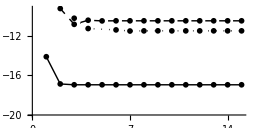
-Graphics-bin number of input sinusoidunwanted spectral power (dB)

../paper_measurements/images/inexact_power.pdf

```mathematica
(* Figure 1 is created by plotting the obtained values *)
thick=Thickness[0.004];
inexactPowerImage=Labeled[ListPlot[computedErrors,Joined->True,Mesh->Full,MeshStyle->Directive[PointSize[0.016],Black],PlotStyle->{{Black,thick},{Dashed,Black,thick},{Dotted,Black,thick},{DotDashed,Black,thick}},AxesOrigin->{0,-20},ImageSize->256,AxesStyle->Black,LabelStyle->{FontSize->10,FontFamily->"Times",Black},AspectRatio->1/2, Ticks->{Table[x,{x,0,20}],Automatic}],{"bin number of input sinusoid", "unwanted spectral power (dB)"},{Bottom, Left}, RotateLabel->True,LabelStyle->{FontSize->10,FontFamily->"Times",Black}]
SetDirectory[NotebookDirectory[]];
Export["../paper_measurements/images/inexact_power.pdf",inexactPowerImage]
```